# Analyzing the Changes in Ideology of the Democratic and Republican Party’s Political Parties from 1900 to 2020

## Introduction

Politics have been an essential part of society since the very beginning, shaping the structure of our government and policies, which in turn affect our lives. The importance of politics have also led to a variety of different political thoughts, such as certain beliefs, policies, and ideas. Throughout the world, people and politicians with similar political thoughts and ideologies have come together to form political entities known as political parties. 

In the United States, the two major political parties are the Democratic Party and the Republican Party. These two political parties, which have existed since the 1800s and have often been political rivals in the US government. Currently, the Democratic Party is known to be a left-wing political party while the Republican Party is considered as a right-wing political party.

However, their political ideologies and ideas have undergone significant shifts throughout the years. This begs the question: Can we analyze how the Democratic and Republican parties’ ideologies have shifted throughout the course of US history?

## Gathering the Data

First, I decided to obtain the political party platforms from The American Presidency Project by UC Santa Barbara. Both the Democratic Party and Republican Party publishes a party platform every four years, which is a long document that explains their stances on political issues and values that will guides the party. Since the party platforms is an official description on the ideologies of the two political parties, these were the primary data that were used for analysis. 

The website only included party platforms up to 2020, as this project was created before the Democratic and Republican Conventions of 2024, which is when they publish their party platform. As a result, this project could only use party platforms up to the year 2020. 

For this project, only party platforms between the years 1900 and 2020, inclusive, will be used for analysis. 

The website was a table of political party platforms by presidential election year with a hyperlink to a separate page that featured the party platform.

The code below gets a list of all of the hyperlinks that are in the main page of the list of party platforms. I used a pattern to selected all of the links connected to the Democratic Party Platform.

```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

The code below does the same action as the previous code, but collects all of the hyperlinks connected to the Republican Party platforms.

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

Using the list of hyperlinks that I obtained for each party, I imported the HTML code from each of the pages. Then, I only took the the text that is inside the HTML div tag with the id “field-docs-content”. This is because this div tag contained the content of the web page, which were the party platforms. It also removes all of the HTML tags that are located within the text. 

The code below obtains all of the Democratic Party’s party platforms.

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

The code below gathers all of the Republican Party’s party platforms.

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],{21;;-1}] & /@ republicans[[2;;31]];
```

This project will not use the 2020 statement from the Republican Party because the party cancelled the 2020 Republican Convention due to the COVID-19 pandemic and the document is an affirmation of the reuse of the 2016 Republican Party platform. As a result, the the 2020 Republican Party platform can be considered as the same as that of 2016.

## Clustering Party Platforms using Principal Components Analysis

When analyzing similarities between texts and clustering, a large amount of dimensions and features will be used, which leads to many issues such as overfitting, scarcity of data, and the inability to represent more than three dimensions. 

Principal Components Analysis is a way around this issue by reducing the number of dimensions to a set of “principal components” that still captures the most important patterns and maximizes the variance within the data. When using text, vector embedding will be used to convert the text into numbers that describes the characteristics of the text. These numbers will be used in the PCA. 

I decided to use PCA in order to visualize how the Democratic and Republican Parties’ party platforms change by plotting them on a 2-dimensional graph and comparing where they lie. 

The first dimension of the graph would be the first principal component, which captures the most variation, and the second dimension would be the second principal component, which captures the most variance that is orthogonal to the first component. Although what the principal components exactly are will not be discussed in the project, it allows for an abstract visualization of the shifts of the political parties.

Using the texts of the party platforms that I had obtained, I decided to create an association where the key was the year and political party and the value was the party platform. This will be used to label the points when we perform the principal components analysis. 

The bottom code creates two associations for Democratic and Republican Party’s platforms and then creates a large association that would include all platforms.

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],{21;;-1}] & /@ republicans[[2;;31]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

The function below returns the color Red if the input ends with “Republican Party” and Blue if the input ends with “Democratic Party”. This is in order to color the points on the graph based on the colors of the political party that the party platform was published by.

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

The code below performs principal component analysis on all of the party platforms and plots each of the party platforms on a graph.

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

In the graph, it is shown that for both the Democratic and Republican Party, the platforms are generally going chronologically from left to right. However, additionally, although the Republican and Democratic Party are at relatively similar positions in the first half of the 20th century, starting from the 1960s and 1970s, a divide between the two parties becomes increasingly clear. This is especially true in the last 20 years, as seen in the graph, where the Republican Party has started to go increasingly higher while the Democratic Party is going increasingly lower. 

This correlates with the ideological shift between the Republican and Democratic Party during the mid-1900s, when the Democratic Party shifted towards supporting civil rights, which alienated its traditional Southern voters who then moved to the Republican Party. The increasing polarization and partisan nature of American politics during the 21st century was also shown in the drastic separation between the two political parties in the graph. 

I also created two separate graphs that shows only the shift of the Republican Party and Democratic Party.

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

One notable exception to the pattern of the shifts of the political parties is the 1984 Democratic Party, which can be shown in the Democratic Party’s graph and the overall graph to be much further away from party platforms from similar time periods. 

The president of the United States during this year was Ronald Reagan, who is known to have transformed the Republican Party and American politics as a whole by becoming the charismatic leader of conservatism and introducing it into mainstream politics. He brought the rise of a new conservative movement in the Republican Party and coupled with his popularity throughout the nation, the Democratic Party may have felt threatened and prompted to be more opposed to the Republican Party than previous years. In fact, the term “Reagan” appears 197 terms in the party platform for that year, referencing an member of the opposing party much more than other party platforms during this time. In the end, the Democratic nominee for that year, Walter Mondale, ended up losing in a massive landslide against Reagan.

## Correlation of Shifts in Specific Issues to Shifts in Left-Right Spectrum

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

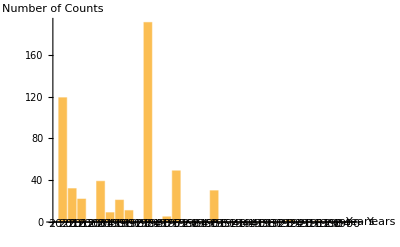

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

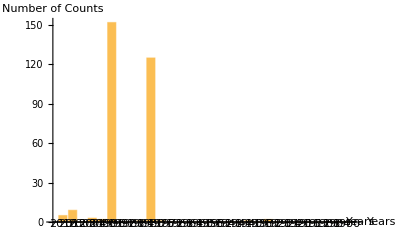

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

## Conclusion

## Future Work

## References

https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3
https://christopherwolfram.com/projects/dimensionality-of-politics/
https://www.britannica.com/topic/political-spectrum
https://www.britannica.com/topic/Democratic-Party
https://www.britannica.com/topic/Republican-Party
https://www.reaganlibrary.gov/reagans/reagan-administration/reagan-presidency
https://www.geeksforgeeks.org/principal-component-analysis-pca/

## Acknowledgements

I would like to thank my mentor, Jack Heseltime, and my teacher’s assistant, Nicoló Monti for their infinite patience, their constant assistance throughout this project, and their willingness to guide me through my first ever research project.

## Cite this Notebook